```mathematica
Exit
```

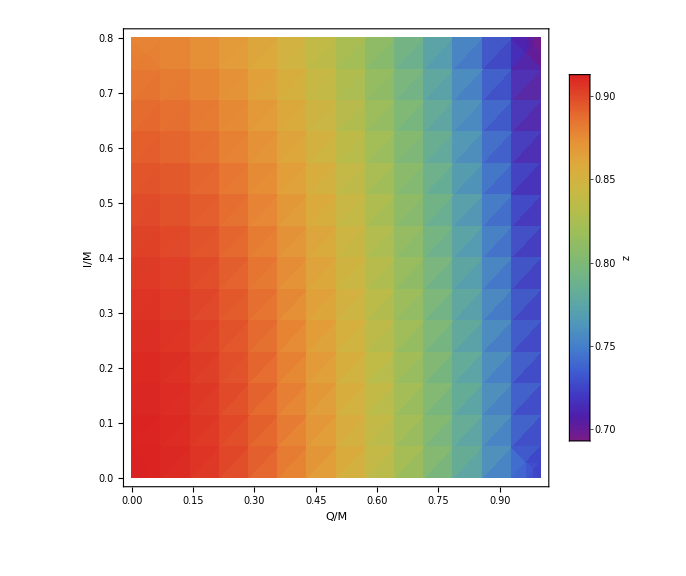
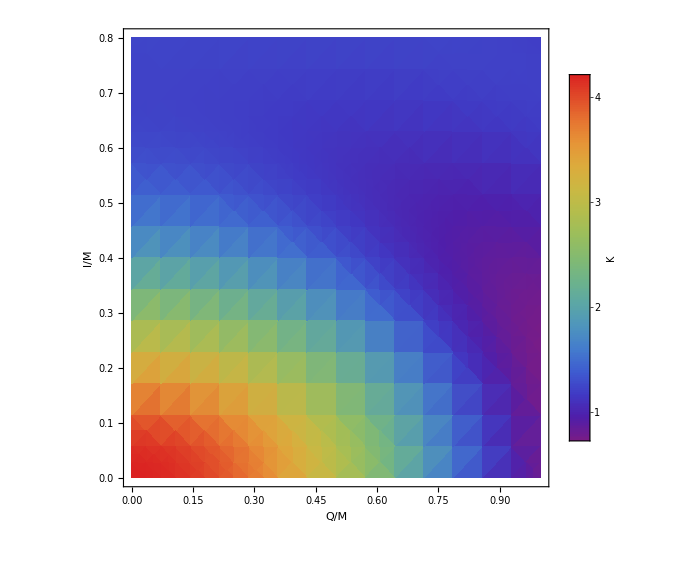
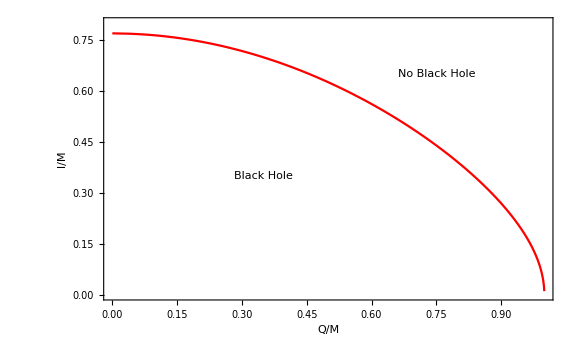
```mathematica
f1=-Graphics-;
f3 = -Graphics-;
f2=-Graphics-;
Show[f1,f2,Epilog->{Text[Style["Black hole", FontSize->20], {0.4,0.4}],Text[Style["No Black hole", FontSize->20], {0.8,0.7}]},PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"\!\(\*SubscriptBox[\(r\), \(ISCO\)]\)",LabelStyle->{Italic,FontFamily->"Helvetica"}],Automatic]]
Show[f3,f2,Epilog->{Text[Style["Black hole", FontSize->20], {0.4,0.4}],Text[Style["No Black hole", FontSize->20], {0.8,0.7}]},PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"\!\(\*SubscriptBox[\(r\), \(ISCO\)]\)",LabelStyle->{Italic,FontFamily->"Helvetica"}],Automatic]]
```

OptionValue::nodef: Unknown option PlotLegends for Graphics.

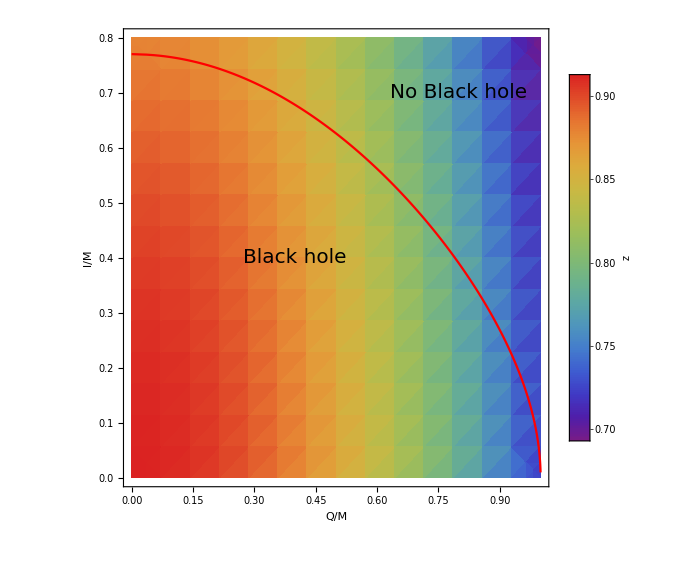

OptionValue::nodef: Unknown option PlotLegends for Graphics.

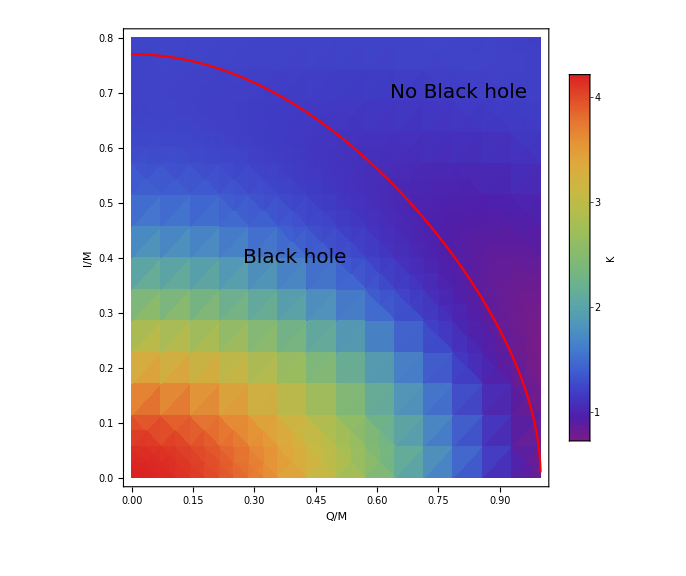

OptionValue::nodef: Unknown option PlotLegends for Graphics.

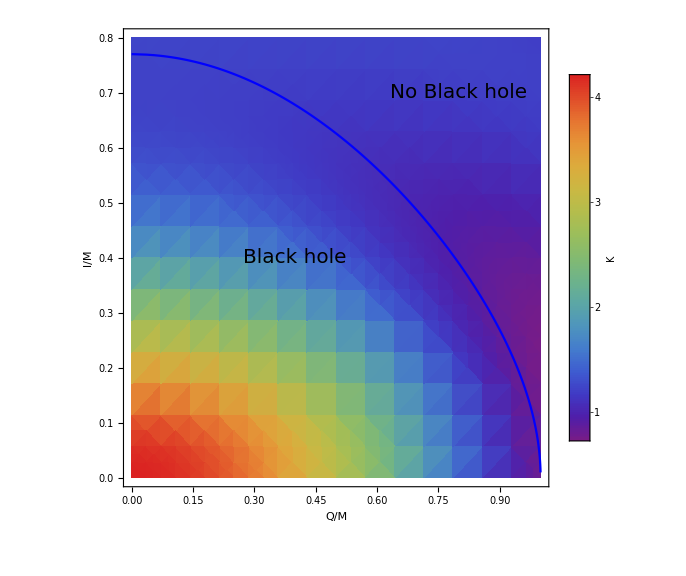

```mathematica
f[r_,Q_,l_]:= 1 - ((2*r-Q^2)*r^2)/(r^4+(2*r+Q^2)l^2);
ll=Table[l,{l,0.0,0.769,0.1}];
QQ=Table[Q/.FindRoot[{(f[r,Q,l]/.{l->ll[[i]]})==0,D[(f[r,Q,l]/.{l->ll[[i]]}),r]==0},{{r,1},{Q,1}}],{i,1,Length[ll]}];
QQll=Table[{QQ[[i]],ll[[i]]},{i,1,Length[ll]}]//TableForm
```

1. | 0.
0.985223 | 0.1
0.943025 | 0.2
0.877306 | 0.3
0.790347 | 0.4
0.681129 | 0.5
0.542645 | 0.6
0.348143 | 0.7

```mathematica
l1=0;
l3=0.2;
l5 = 0.4;
M=1;
```

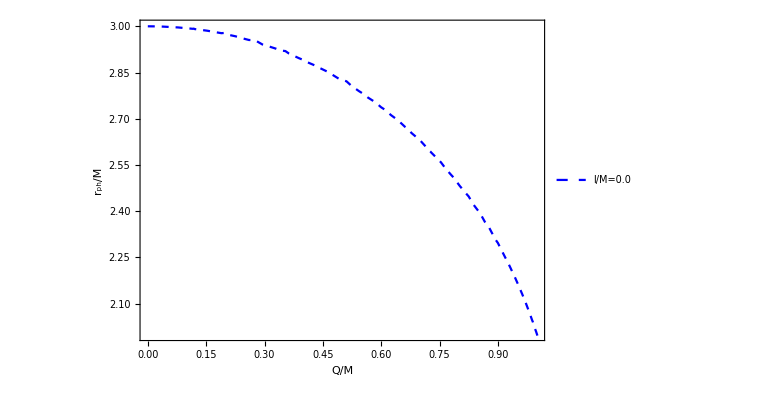

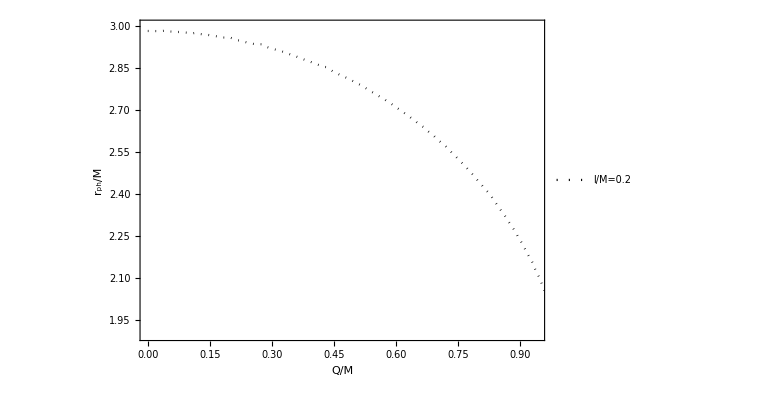

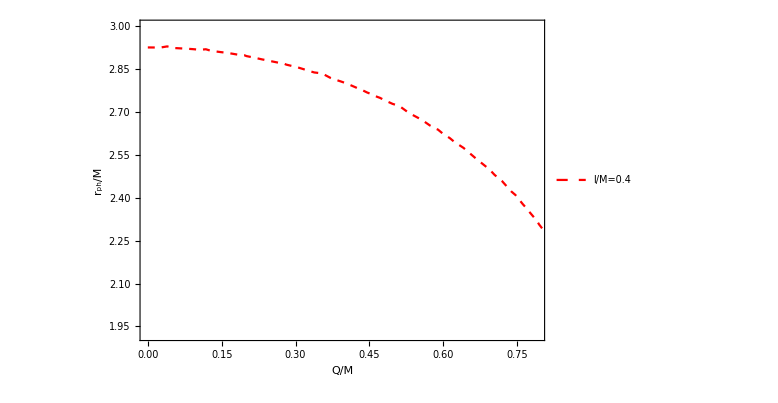

```mathematica
(l^4 (Q^2+2 M r)^2+r^6 (2 Q^2+r (-3 M+r))+2 l^2 r^3 (Q^2 r+M (Q^2+2 r^2)))/r^3 (r^4+l^2 (Q^2+2 M r)) (l^2 (Q^2+2 M r)+r^2 (Q^2+r (-2 M+r)));
ContourPlot[{(l1^4 (Q^2+2 M r)^2+r^6 (2 Q^2+r (-3 M+r))+2 l1^2 r^3 (Q^2 r+M (Q^2+2 r^2)))/(r^3 (r^4+l1^2 (Q^2+2 M r)) (l1^2 (Q^2+2 M r)+r^2 (Q^2+r (-2 M+r))))==0},{Q,0,1.1},{r,0.0,3.23},PlotRange-> {{0,1},{2,3}},PlotLegends->Placed[{"l/M=0.0","l/M=0.2","l/M=0.4"},{Scaled[{0.7,0.9}],{0,0.5}}],ContourStyle->{{Dashed,Blue}},FrameLabel->{" Q/M","r_ph/M"},AspectRatio->0.7,Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large]
ContourPlot[{ (l3^4 (Q^2+2 M r)^2+r^6 (2 Q^2+r (-3 M+r))+2 l3^2 r^3 (Q^2 r+M (Q^2+2 r^2)))/(r^3 (r^4+l3^2 (Q^2+2 M r)) (l3^2 (Q^2+2 M r)+r^2 (Q^2+r (-2 M+r))))==0},{Q,0,1.1},{r,0.0,3.23},PlotRange-> {{0,0.94},{1.9,3}},PlotLegends->Placed[{"l/M=0.2","l/M=0.2","l/M=0.4"},{Scaled[{0.7,0.8}],{0,0.5}}],ContourStyle->{{Dotted,Black}},FrameLabel->{" Q/M","r_ph/M"},AspectRatio->0.7,Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large]
ContourPlot[{(l5^4 (Q^2+2 M r)^2+r^6 (2 Q^2+r (-3 M+r))+2 l5^2 r^3 (Q^2 r+M (Q^2+2 r^2)))/(r^3 (r^4+l5^2 (Q^2+2 M r)) (l5^2 (Q^2+2 M r)+r^2 (Q^2+r (-2 M+r))))==0},{Q,0,1.1},{r,0.0,3.23},PlotRange-> {{0,0.79},{1.922,3}},PlotLegends->Placed[{"l/M=0.4","l/M=0.2","l/M=0.4"},{Scaled[{0.7,0.7}],{0,0.5}}],ContourStyle->{{Dashed,Red}},FrameLabel->{" Q/M","r_ph/M"},AspectRatio->0.7,Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},ImageSize->Large]
```